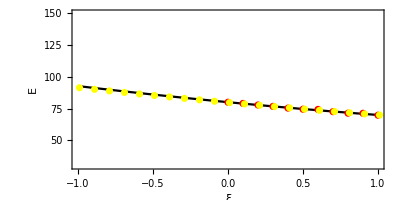

```mathematica
esfree={{1.01,69.95},{0.91,70.84},{0.81,71.75},{0.71,72.68},{0.61,73.63},{0.51,74.60},{0.4099999999999999,75.58},{0.30999999999999994,76.59},{0.20999999999999996,77.61},{0.10999999999999999,78.65},{0.010000000000000009,79.71},{-0.09000000000000008,80.79},{-0.19000000000000017,81.89},{-0.29000000000000004,83.01},{-0.3900000000000001,84.15},{-0.49,85.31},{-0.5900000000000001,86.48},{-0.6900000000000002,87.68},{-0.79,88.90},{-0.8900000000000001,90.13},{-0.99,91.39}};
es={{1.,69.82},{0.9,71.33},{0.8,71.41},{0.7,72.61},{0.6,74.37},
{0.5,74.53},{0.3999999999999999,75.39},{0.29999999999999993,76.76},{0.19999999999999996,77.83},{0.09999999999999998,79.08},{0.,80.00}};
f100=642.4588820769225-73.25085811888027 x-2.4720416083918693 x^2;
f16=80.05208656643349-11.340731776223691 x+1.2971146853146518 x^2;
Show[Plot[f16,{x,-1,1},PlotRange->{30,150},PlotStyle->Black],ListPlot[{es,esfree},PlotStyle->{Red,Yellow,Blue}],Frame->True,FrameLabel->{{HoldForm["E"],None},{HoldForm[ξ],None}},PlotLabel->None,LabelStyle->{10,GrayLevel[0]},AspectRatio->0.5]
```

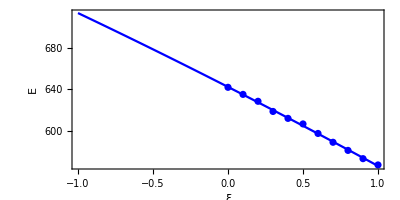

```mathematica
es100={{1.,567.700834},{0.9,573.716988},{0.8,581.623449},{0.7,589.413144},{0.6,597.874616},{0.5,606.985037},{0.3999999999999999,612.313939},{0.29999999999999993,618.947511},{0.19999999999999996,628.693279},{0.09999999999999998,635.302658},{0.,642.079168}};
f100=642.4588820769225-73.25085811888027 x-2.4720416083918693 x^2;
f16=80.05208656643349-11.340731776223691 x+1.2971146853146518 x^2;
Show[Plot[f100,{x,-1,1},PlotStyle->Blue],ListPlot[{es100},PlotStyle->{Blue}],Frame->True,FrameLabel->{{HoldForm["E"],None},{HoldForm[ξ],None}},PlotLabel->None,LabelStyle->{10,GrayLevel[0]},AspectRatio->0.5]
```